```mathematica
D[f[x],x]==λ f[x]
```

f'[x]==λ f[x]

```mathematica
DSolve[f'[x]==λ f[x],{f[x]},{x}]
```

{{f[x]→ⅇ^(x λ) C[1]}}

```mathematica
With[{f=Identity},
f'[x]==λ f[x]]
```

1==x λ

```mathematica
Reduce[1==x λ]
```

λ≠0&&x==1/λ

```mathematica
SolveAlways[1==x λ,{x}]
```

{}

```mathematica
Exp[1==x λ]
```

ⅇ^(1==x λ)

```mathematica
Exp[1]==Exp[x λ]
```

ⅇ==ⅇ^(x λ)

```mathematica
Conjugate[1]
```

1

```mathematica
Conjugate[α+β ⅈ]
```

Conjugate[α]-ⅈ Conjugate[β]

```mathematica
ComplexExpand[Conjugate[α]-ⅈ Conjugate[β],{α,β},TargetFunctions->Re]
```

ⅈ β+Re[α]+ⅈ (ⅈ α-ⅈ Re[α]-Re[β])-ⅈ Re[β]

```mathematica
D[H[t,x],{t,2}]==c^2 D[H[t,x],{x,2}]
```

H^(2,0)[t,x]==c^2 H^(0,2)[t,x]

```mathematica
DSolve[Derivative[2,0][H][t,x]==c^2 Derivative[0,2][H][t,x],{H[t,x],H[t,x]},{t,x}]
```

{{H[t,x]→C[1][-√(c^2) t+x]+C[2][√(c^2) t+x]}}

```mathematica
D[H[t,x],{t,2}]==1D[H[t,x],{x,2}]
```

H^(2,0)[t,x]==H^(0,2)[t,x]

```mathematica
DSolve[Derivative[2,0][H][t,x]==Derivative[0,2][H][t,x],{H[t,x],H[t,x]},{t,x}]
```

{{H[t,x]→C[1][-t+x]+C[2][t+x]}}

```mathematica
Laplacian[f[x,y],{x,y}]==λ f[x,y]
```

f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y]

```mathematica
DSolve[Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]
```

DSolve[f^(0,2)[x,y]+f^(2,0)[x,y]==λ f[x,y],{f[x,y],f[x,y]},{x,y}]

```mathematica
Solve[
Derivative[0,2][f][x,y]+Derivative[2,0][f][x,y]==λ f[x,y],f[x,y]]
```

{{f[x,y]→(f^(0,2)[x,y]+f^(2,0)[x,y])/λ}}

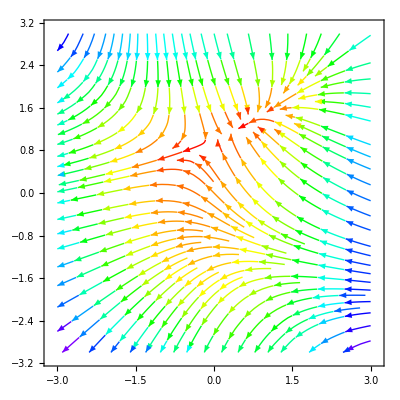

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},StreamColorFunction->Hue]
```

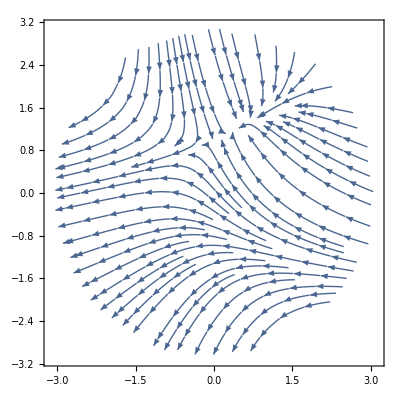

```mathematica
StreamPlot[{
-1-x^2+y
,
1+x-y^2
},{x,y}∈Disk[{0,0},3]]
```

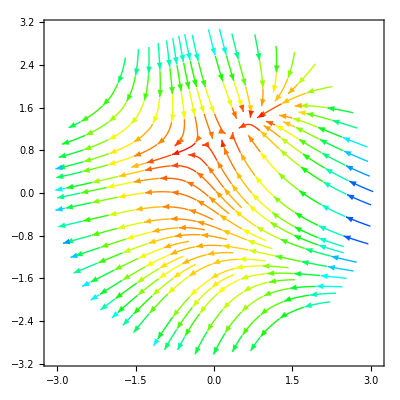

```mathematica
StreamPlot[{
-1-x^2+y
,
1+x-y^2
},{x,y}∈Disk[{0,0},3], StreamColorFunction->Hue]
```

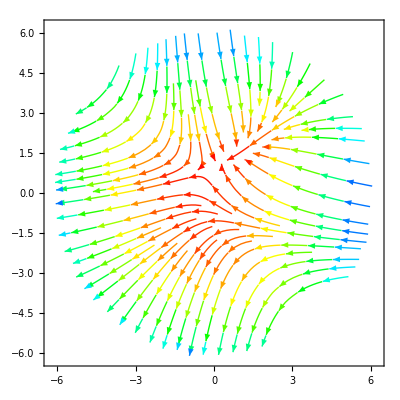

```mathematica
StreamPlot[{
-1-x^2+y
,
1+x-y^2
},{x,y}∈Disk[{0,0},6]
, StreamColorFunction->Hue]
```

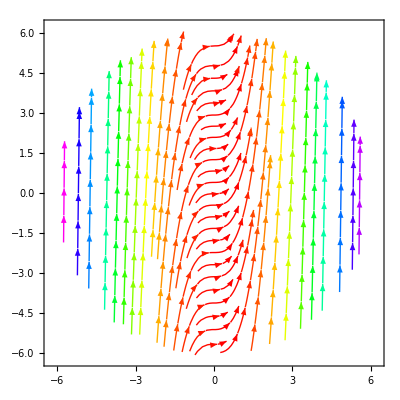

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Disk[{0,0},6],
 StreamColorFunction->Hue]
```

```mathematica
Rectangle[]
```

Rectangle[{0,0}]

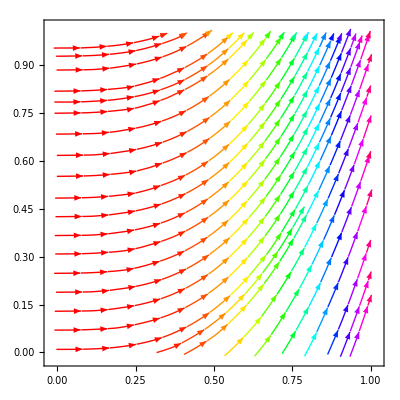

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[],
 StreamColorFunction->Hue]
```

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{{-1,-1},{1,1}}],
 StreamColorFunction->Hue]
```

StreamPlot::idomdim: {x,y}∈Rectangle[{{-1,-1},{1,1}}] does not have a valid dimension as a plotting domain.

StreamPlot[{1,3 x^2},{x,y}∈Rectangle[{{-1,-1},{1,1}}],StreamColorFunction→Hue]

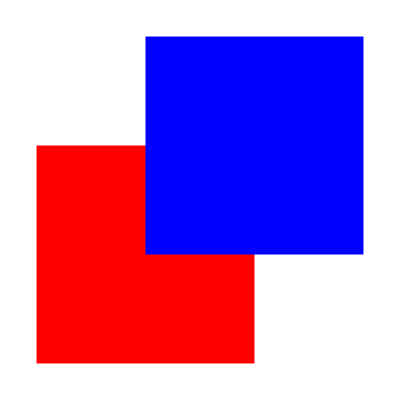

```mathematica
Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]
```

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{0,0}],
 StreamColorFunction->Hue]
```

-Graphics-

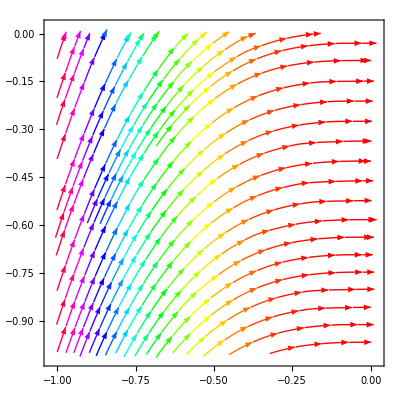

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-1,-1}],
 StreamColorFunction->Hue]
```

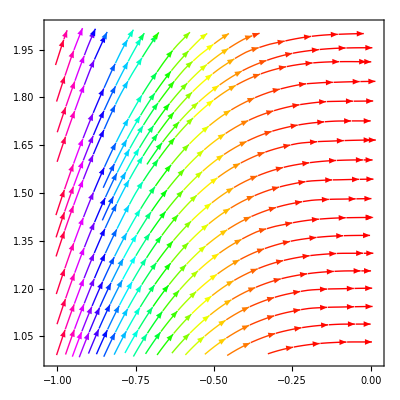

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-1,1}],
 StreamColorFunction->Hue]
```

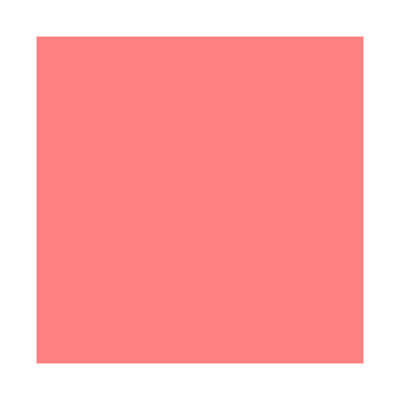
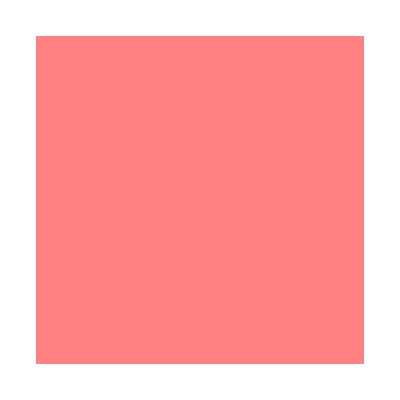
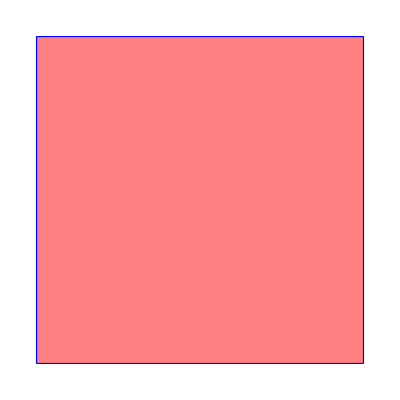
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Graphics[{Pink,Rectangle[]}],Graphics[{EdgeForm[Thick],Pink,Rectangle[]}],Graphics[{EdgeForm[Dashed],Pink,Rectangle[]}],Graphics[{EdgeForm[Directive[Thick,Dashed,Blue]],Pink,Rectangle[]}]}
```

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{{-1,-1},{2,2}}],
 StreamColorFunction->Hue]
```

StreamPlot::idomdim: {x,y}∈Rectangle[{{-1,-1},{2,2}}] does not have a valid dimension as a plotting domain.

StreamPlot[{1,3 x^2},{x,y}∈Rectangle[{{-1,-1},{2,2}}],StreamColorFunction→Hue]

```mathematica
Animate[With[{q=Quotient[θ,π/2],m=Mod[θ,π/2]},Graphics[{EdgeForm[Black],LightGray,Rotate[Rectangle[{q,0}],-m,{q+1,0}]},Axes->{True,False},PlotRange->{{-.5,5.5},{-0.5,1.5}},ImageSize->350]],{θ,0,2Pi},AnimationRunning->False,AnimationDirection->ForwardBackward,DefaultDuration->2]
```

```mathematica
Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]
```

-Graphics-

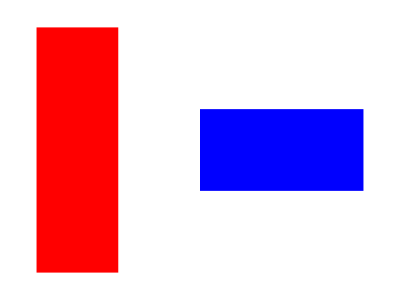

```mathematica
Graphics[{Red,Rectangle[{0,0},{1,3}],Blue,Rectangle[{2,1},{4,2}]}]
```

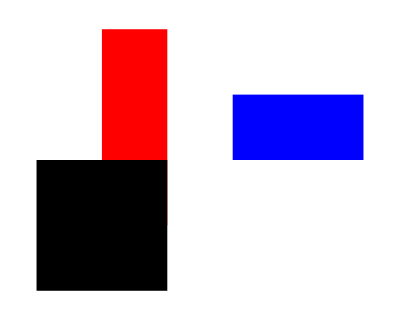

```mathematica
Graphics[{
Red,Rectangle[{0,0},{1,3}],
Blue,Rectangle[{2,1},{4,2}],
Black,Rectangle[{-1,-1},{1,1}]
}]
```

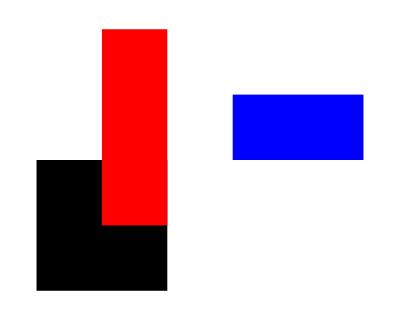

```mathematica
Graphics[{
Black,Rectangle[{-1,-1},{1,1}],
Red,Rectangle[{0,0},{1,3}],
Blue,Rectangle[{2,1},{4,2}]
}]
```

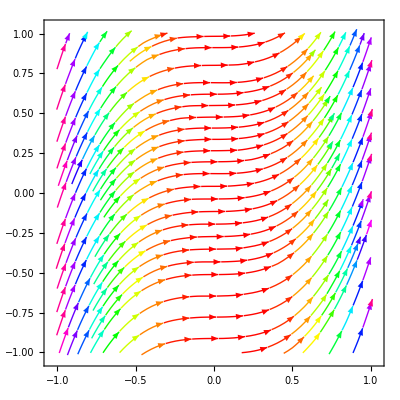

```mathematica
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-1,-1},{1,1}],
 StreamColorFunction->Hue]
```

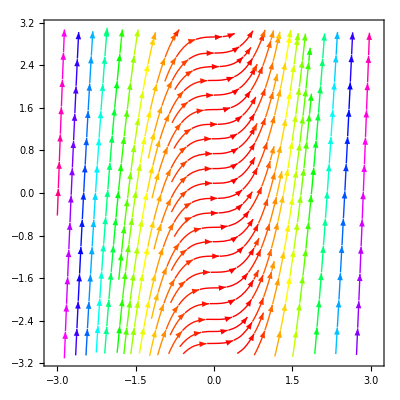

```mathematica
With[{a=3},
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-a,-a},{a,a}],
 StreamColorFunction->Hue]]
```

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].Normalize[{0,0}],
x∈Reals]
```

0

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].Normalize[{1,1}],
x∈Reals]
```

(1+3 x^2)/(√(2+18 x^4))

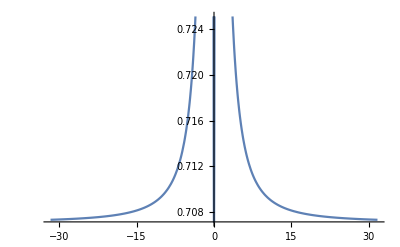

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-31.72,31.72}]
```

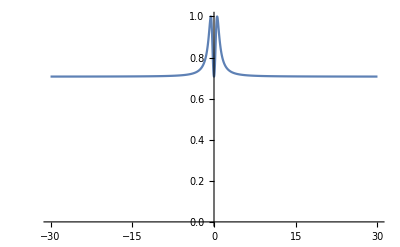

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-30,30}, PlotRange->{0, 1}]
```

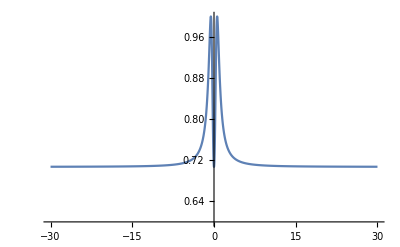

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-30,30}, PlotRange->{0.6, 1}]
```

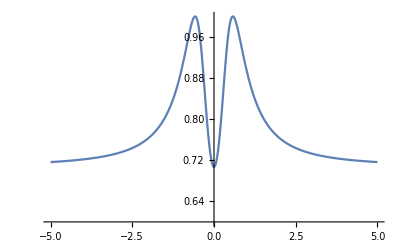

```mathematica
Plot[(1+3 x^2)/(√(2+18 x^4)),{x,-5,5}, PlotRange->{0.6, 1}]
```

```mathematica
FinancialData["^N225", "Price"]
```

FinancialData::notent: ^N225 is not a known entity, class, or tag for FinancialData. Use FinancialData[] for a list of entities.

Missing[NotAvailable]

```mathematica
(1+3 x^2)/(√(2+18 x^4))==1
```

(1+3 x^2)/(√(2+18 x^4))==1

```mathematica
Reduce[(1+3 x^2)/(√(2+18 x^4))==1]
```

x==-1/(√3)||x==1/(√3)

```mathematica
With[{a=3},
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-a,-a},{a,a}],
 StreamColorFunction->Hue]]
```

-Graphics-

```mathematica
CountryData["UnitedStates", "ExportPartners"]
```

{Canada,Mexico,China,Japan,United Kingdom,Germany}

```mathematica
CountryData["UnitedStates", "ExportPartnersFractions"]
```

{Canada→0.201,Mexico→0.117,China→0.055,Japan→0.051,United Kingdom→0.041,Germany→0.042}

```mathematica
CountryData["UnitedStates", "ExportValue"]CountryData["UnitedStates", "ExportPartnersFractions"]
```

{(2214566000000 $) (Canada→0.201),(2214566000000 $) (Mexico→0.117),(2214566000000 $) (China→0.055),(2214566000000 $) (Japan→0.051),(2214566000000 $) (United Kingdom→0.041),(2214566000000 $) (Germany→0.042)}

```mathematica
Map[
First[#]->CountryData["UnitedStates", "ExportValue"] Last[#] &,
CountryData["UnitedStates", "ExportPartnersFractions"]]
```

{Canada→4.45128×10^11 $,Mexico→2.59104×10^11 $,China→1.21801×10^11 $,Japan→1.12943×10^11 $,United Kingdom→9.07972×10^10 $,Germany→9.30118×10^10 $}

```mathematica
Grid@
ReverseSortBy[
Map[
{First[#],CountryData["UnitedStates", "ExportValue"] Last[#] }&,
CountryData["UnitedStates", "ExportPartnersFractions"]],
Last]
```

Canada | 4.45128×10^11 $
Mexico | 2.59104×10^11 $
China | 1.21801×10^11 $
Japan | 1.12943×10^11 $
Germany | 9.30118×10^10 $
United Kingdom | 9.07972×10^10 $

```mathematica
With[{a=3},
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-a,-a},{a,a}],
 StreamColorFunction->Hue]]
```

-Graphics-

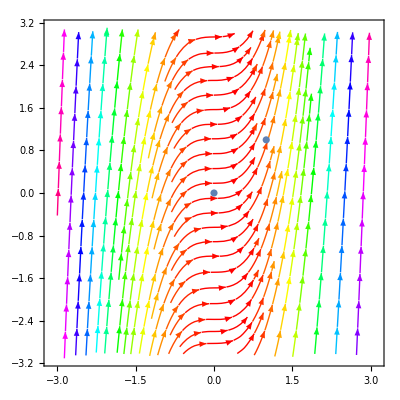

```mathematica
With[{a=3},
Show[{
StreamPlot[{
1,
3 x^2
},{x,y}∈Rectangle[{-a,-a},{a,a}],
 StreamColorFunction->Hue],
ListPlot[{{0,0},{1,1}}]
}]]
```

```mathematica
FullSimplify[
Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}], {x,f[x],f'[x]}∈Reals]
```

(1+3 x^2 f'[x])/(√((1+9 x^4) (1+f'[x]^2)))

```mathematica
FullSimplify[
1==Normalize[{1,3 x^2}].
Normalize[{1,f'[x]}], {x,f[x],f'[x]}∈Reals]
```

√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x]

```mathematica
DSolve[√((1+9 x^4) (1+f'[x]^2))==1+3 x^2 f'[x],{f[x]},{x}]
```

{{f[x]→x^3+C[1]}}

```mathematica
FullSimplify[
1==Normalize[{1,g'[x]}].
Normalize[{1,f'[x]}], {x,f[x], g[x], g'[x],f'[x]}∈Reals]
```

√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x]

```mathematica
DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x],g[x]},{x}]

```mathematica
Solve[
√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x], {f'[x]}]
```

{{f'[x]→g'[x]}}

```mathematica
Solve[
√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x], {f'[x]}]
```

```mathematica
DSolve[{√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x], f[0]==0, f[1]==1}, {f[x]},x]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
CountryData["UnitedStates"]
```

United States

```mathematica
Integrate[{f'[x],g'[x]},x]
```

{f[x],g[x]}

```mathematica
FullSimplify[
1==Normalize[{1,g'[x]}].
Normalize[{1,f'[x]}], {x,f[x], g[x], g'[x],f'[x]}∈Reals]
```

√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x]

```mathematica
Solve[
FullSimplify[
1==Normalize[{1,g'[x]}].
Normalize[{1,f'[x]}], {x,f[x], g[x], g'[x],f'[x]}∈Reals]
,{f'[x]}]
```

{{f'[x]→g'[x]}}

```mathematica
FullSimplify[
1==Normalize[{1,g'[x]}].
Normalize[{1,f'[x]}], {x,f[x], g[x], g'[x],f'[x]}∈Reals]
```

```mathematica
Solve[
FullSimplify[
1==Normalize[{h'[x],g'[x]}].
Normalize[{1,f'[x]}], {x,f[x],h[x],h'[x], g[x], g'[x],f'[x]}∈Reals]
,{f'[x]}]
```

{{f'[x]→g'[x]/h'[x]}}

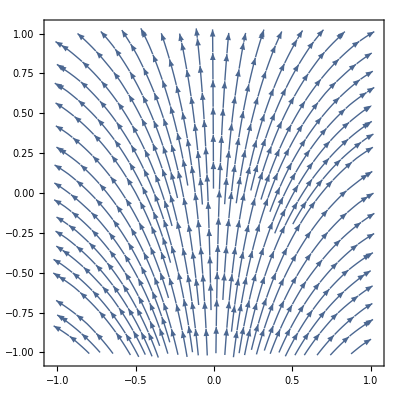

```mathematica
StreamPlot[
{Sin[x], Cos[x]},
{x,y}∈Rectangle[{-1,-1},{1,1}]]
```

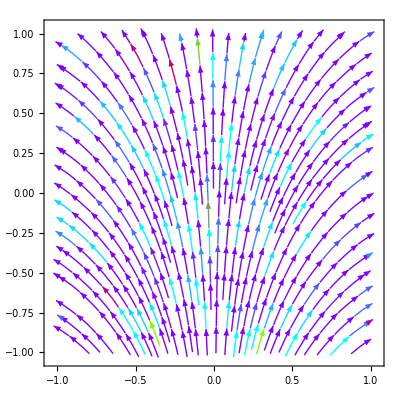

```mathematica
StreamPlot[
{Sin[x], Cos[x]},
{x,y}∈Rectangle[{-1,-1},{1,1}],
StreamColorFunction->Hue]
```

```mathematica
StreamPlot[
{Sin[x], Cos[x]},
{x,y}∈Rectangle[{-1,-1},{1,1}],
StreamColorFunction->Hue]
```

```mathematica
Solve[
FullSimplify[
1==Normalize[{Sin[x],Cos[x]}].
Normalize[{1,f'[x]}], {x,f[x],h[x],h'[x], g[x], g'[x],f'[x]}∈Reals]
,{f'[x]}]
```

{{f'[x]→Cot[x]}}

```mathematica
Integrate[{Sin[x], Cos[x]},x]
```

{-Cos[x],Sin[x]}

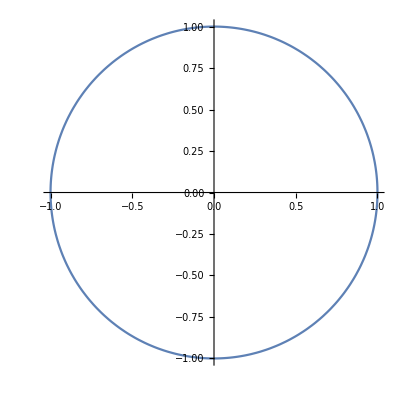

```mathematica
ParametricPlot[
{-Cos[t],Sin[t]},
{t, 0, 2π}]
```

```mathematica
Solve[
FullSimplify[
1==Normalize[{Sin[x],Cos[x]}].
Normalize[{1,f'[x]}], {x,f[x],f'[x]}∈Reals]
,{f'[x]}]
```

{{f'[x]→Cot[x]}}

```mathematica
Solve[
FullSimplify[
1==Normalize[{Sin[x],Cos[x]}].
Normalize[{1,f'[x]}], {x,f[x],f'[x]}∈Reals]
,{f[x]}]
```

{}

```mathematica
Last@
First@
Last@
Solve[
FullSimplify[
1==Normalize[{Sin[x],Cos[x]}].
Normalize[{1,f'[x]}], {x,f[x],f'[x]}∈Reals]
,{f'[x]}]
```

Cot[x]

```mathematica
Integrate[
Last@
First@
Last@
Solve[
FullSimplify[
1==Normalize[{Sin[x],Cos[x]}].
Normalize[{1,f'[x]}], {x,f[x],f'[x]}∈Reals]
,{f'[x]}]
,x]
```

Log[Sin[x]]

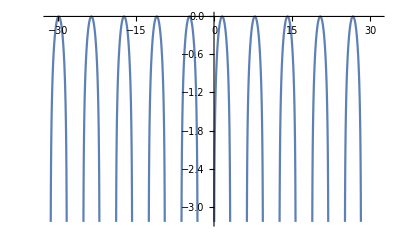

```mathematica
Plot[Log[Sin[x]],{x,-10 π,10 π}]
```

```mathematica
<<VariationalMethods`
```

```mathematica
ToCharacterCode[%82]
```

{{63425,63433,63432,82,111,119,66,111,120,91,123,34,78,86,97,114,105,97,116,105,111,110,97,108,66,111,117,110,100,34,44,32,34,91,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,102,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,34,91,34,44,32,82,111,119,66,111,120,91,123,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,82,111,119,66,111,120,91,123,34,93,34,44,32,34,44,34,125,93,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,109,105,110,34,44,32,34,84,73,34,93,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,109,97,120,34,44,32,34,84,73,34,93,93,125,93,44,32,34,125,34,125,93,125,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,116,34,44,32,34,84,73,34,93,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,8230,34,44,32,34,84,73,34,93,125,93,44,32,34,93,34,125,93,125,93,125,93,63424,32,110,117,109,101,114,105,99,97,108,108,121,32,115,101,97,114,99,104,101,115,32,102,111,114,32,118,97,108,117,101,115,32,111,102,32,116,104,101,32,112,97,114,97,109,101,116,101,114,115,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,63424,44,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,63424,44,32,46,46,46,32,111,102,32,97,32,116,114,105,97,108,32,102,117,110,99,116,105,111,110,32,63425,63433,63432,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,116,34,44,32,34,84,73,34,93,93,63424,44,32,115,116,97,114,116,105,110,103,32,102,114,111,109,32,63425,63433,63432,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,34,61,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,63424,44,32,63425,63433,63432,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,34,61,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,63424,44,32,46,46,46,44,32,116,104,97,116,32,101,120,116,114,101,109,105,122,101,32,116,104,101,32,102,117,110,99,116,105,111,110,97,108,32,63425,63433,63432,82,111,119,66,111,120,91,123,83,117,98,115,117,112,101,114,115,99,114,105,112,116,66,111,120,91,34,8747,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,34,120,34,44,32,83,116,121,108,101,66,111,120,91,34,109,105,110,34,44,32,70,111,110,116,83,108,97,110,116,32,45,62,32,34,73,116,97,108,105,99,34,93,93,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,34,120,34,44,32,83,116,121,108,101,66,111,120,91,34,109,97,120,34,44,32,70,111,110,116,83,108,97,110,116,32,45,62,32,34,73,116,97,108,105,99,34,93,93,93,44,32,82,111,119,66,111,120,91,123,34,102,34,44,32,82,111,119,66,111,120,91,123,34,63308,34,44,32,34,120,34,125,93,125,93,125,93,63424,44,32,119,104,101,114,101,32,116,104,101,32,105,110,116,101,103,114,97,110,100,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,102,34,44,32,34,84,73,34,93,63424,32,105,115,32,97,32,102,117,110,99,116,105,111,110,32,111,102,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,63424,44,32,105,116,115,32,100,101,114,105,118,97,116,105,118,101,115,44,32,97,110,100,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,63424,46,10,63425,63433,63432,82,111,119,66,111,120,91,123,34,78,86,97,114,105,97,116,105,111,110,97,108,66,111,117,110,100,34,44,32,34,91,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,102,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,34,91,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,121,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,8230,34,44,32,34,84,82,34,93,125,93,44,32,34,93,34,125,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,109,105,110,34,44,32,34,84,73,34,93,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,109,97,120,34,44,32,34,84,73,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,8230,34,44,32,34,84,82,34,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,116,34,44,32,34,84,73,34,93,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,8230,34,44,32,34,84,82,34,93,125,93,44,32,34,93,34,125,93,63424,32,115,101,97,114,99,104,101,115,32,102,111,114,32,118,97,108,117,101,115,32,111,102,32,116,104,101,32,112,97,114,97,109,101,116,101,114,115,32,111,102,32,97,32,116,114,105,97,108,32,102,117,110,99,116,105,111,110,32,111,102,32,116,119,111,32,111,114,32,109,111,114,101,32,118,97,114,105,97,98,108,101,115,46,10,63425,63433,63432,82,111,119,66,111,120,91,123,34,78,86,97,114,105,97,116,105,111,110,97,108,66,111,117,110,100,34,44,32,34,91,34,44,32,82,111,119,66,111,120,91,123,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,102,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,103,34,44,32,34,84,73,34,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,34,91,34,44,32,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,34,93,34,125,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,109,105,110,34,44,32,34,84,73,34,93,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,109,97,120,34,44,32,34,84,73,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,116,34,44,32,34,84,73,34,93,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,97,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,82,111,119,66,111,120,91,123,34,123,34,44,32,82,111,119,66,111,120,91,123,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,34,44,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,83,116,121,108,101,66,111,120,91,34,98,34,44,32,34,84,73,34,93,44,32,83,116,121,108,101,66,111,120,91,34,48,34,44,32,34,84,82,34,93,93,125,93,44,32,34,125,34,125,93,44,32,34,44,34,44,32,83,116,121,108,101,66,111,120,91,34,8230,34,44,32,34,84,82,34,93,125,93,44,32,34,93,34,125,93,63424,32,115,101,97,114,99,104,101,115,32,102,111,114,32,118,97,108,117,101,115,32,111,102,32,116,104,101,32,112,97,114,97,109,101,116,101,114,115,32,116,104,97,116,32,101,120,116,114,101,109,105,122,101,32,116,104,101,32,114,97,116,105,111,32,63425,63433,63432,82,111,119,66,111,120,91,123,83,117,98,115,117,112,101,114,115,99,114,105,112,116,66,111,120,91,34,8747,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,34,120,34,44,32,83,116,121,108,101,66,111,120,91,34,109,105,110,34,44,32,70,111,110,116,83,108,97,110,116,32,45,62,32,34,73,116,97,108,105,99,34,93,93,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,34,120,34,44,32,83,116,121,108,101,66,111,120,91,34,109,97,120,34,44,32,70,111,110,116,83,108,97,110,116,32,45,62,32,34,73,116,97,108,105,99,34,93,93,93,44,32,82,111,119,66,111,120,91,123,34,102,34,44,32,82,111,119,66,111,120,91,123,82,111,119,66,111,120,91,123,34,63308,34,44,32,34,120,34,125,93,44,32,34,47,34,44,32,82,111,119,66,111,120,91,123,83,117,98,115,117,112,101,114,115,99,114,105,112,116,66,111,120,91,34,8747,34,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,34,120,34,44,32,83,116,121,108,101,66,111,120,91,34,109,105,110,34,44,32,70,111,110,116,83,108,97,110,116,32,45,62,32,34,73,116,97,108,105,99,34,93,93,44,32,83,117,98,115,99,114,105,112,116,66,111,120,91,34,120,34,44,32,83,116,121,108,101,66,111,120,91,34,109,97,120,34,44,32,70,111,110,116,83,108,97,110,116,32,45,62,32,34,73,116,97,108,105,99,34,93,93,93,44,32,82,111,119,66,111,120,91,123,34,103,34,44,32,82,111,119,66,111,120,91,123,34,63308,34,44,32,34,120,34,125,93,125,93,125,93,125,93,125,93,125,93,63424,44,32,119,104,101,114,101,32,116,104,101,32,105,110,116,101,103,114,97,110,100,115,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,102,34,44,32,34,84,73,34,93,63424,32,97,110,100,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,103,34,44,32,34,84,73,34,93,63424,32,97,114,101,32,102,117,110,99,116,105,111,110,115,32,111,102,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,117,34,44,32,34,84,73,34,93,63424,44,32,105,116,115,32,100,101,114,105,118,97,116,105,118,101,115,44,32,97,110,100,32,63425,63433,63432,83,116,121,108,101,66,111,120,91,34,120,34,44,32,34,84,73,34,93,63424,46}}

```mathematica
VariationalD[y[x] √(1+y'[x]^2),y[x],x]
```

(1+y'[x]^2-y[x] y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
VariationalD[y'[x],y[x],x]
```

0

```mathematica
VariationalD[ √(1+y'[x]^2),y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
D[ √(1+y'[x]^2),y'[x]]
```

y'[x]/(√(1+y'[x]^2))

```mathematica
D[ √(1+y'[x]^2),y[x]]
```

0

```mathematica
y'[x]/(√(1+y'[x]^2))==0
```

y'[x]/(√(1+y'[x]^2))==0

```mathematica
DSolve[y'[x]/(√(1+y'[x]^2))==0,{y[x]},{x}]
```

{{y[x]→C[1]}}

```mathematica
D[D[ √(1+y'[x]^2),y'[x]],x]
```

-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))

```mathematica
D[D[ √(1+y'[x]^2),y'[x]],x]==0
```

-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))==0

```mathematica
DSolve[-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))==0,{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
VariationalD[ √(1+y'[x]^2),y[x],x]
```

-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))==-y''[x]/((1+y'[x]^2)^(3/2))
```

-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))==-y''[x]/((1+y'[x]^2)^(3/2))

```mathematica
DSolve[-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))==-y''[x]/((1+y'[x]^2)^(3/2)),{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
ExpandAll[-(y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))+y''[x]/(√(1+y'[x]^2))]
```

y''[x]/(√(1+y'[x]^2))-(y'[x]^2 y''[x])/(√(1+y'[x]^2)+y'[x]^2 √(1+y'[x]^2))

```mathematica
D[L[x,f[x],f'[x]],f[x]]-D[D[L[x,f[x],f'[x]],y'[x]],x]==0
```

L^(0,1,0)[x,f[x],f'[x]]==0

```mathematica
DSolve[Derivative[0,1,0][L][x,f[x],f'[x]]==0,{f[x],L[x,f[x],f'[x]]},{x}]
```

DSolve::ivar2: The independent variable x should not appear in two different arguments of the dependent variable L[x,f[x],f'[x]].

DSolve[L^(0,1,0)[x,f[x],f'[x]]==0,{f[x],L[x,f[x],f'[x]]},{x}]

```mathematica
-y''[x]/((1+y'[x]^2)^(3/2))==0
```

-y''[x]/((1+y'[x]^2)^(3/2))==0

```mathematica
DSolve[-y''[x]/((1+y'[x]^2)^(3/2))==0,{y[x],y[x]},{x}]
```

{{y[x]→C[1]+x C[2]}}

```mathematica
VariationalD[y'[x] √(1+y'[x]^2),y[x],x]
```

-(y'[x] (3+2 y'[x]^2) y''[x])/((1+y'[x]^2)^(3/2))

```mathematica
DSolve[VariationalD[y'[x] √(1+y'[x]^2),y[x],x]==0, {y[x]},{x}]
```

{{y[x]→C[1]},{y[x]→-ⅈ √(3/2) x+C[1]},{y[x]→ⅈ √(3/2) x+C[1]},{y[x]→C[1]+x C[2]}}

```mathematica
VariationalD[ √(D[u[x,y],x]^2+D[u[x,y],y]^2),u[x,y],{x,y}]
```

(-u^(0,2)[x,y] (u^(1,0)[x,y])^2+u^(0,1)[x,y] (2 u^(1,0)[x,y] u^(1,1)[x,y]-u^(0,1)[x,y] u^(2,0)[x,y]))/(((u^(0,1)[x,y])^2+(u^(1,0)[x,y])^2)^(3/2))

```mathematica
VariationalD[ √(D[u[x,y],x]^2+D[u[x,y],y]^2),u[x,y],{x,y}]==0
```

(-u^(0,2)[x,y] (u^(1,0)[x,y])^2+u^(0,1)[x,y] (2 u^(1,0)[x,y] u^(1,1)[x,y]-u^(0,1)[x,y] u^(2,0)[x,y]))/(((u^(0,1)[x,y])^2+(u^(1,0)[x,y])^2)^(3/2))==0

```mathematica
DSolve[%105,{u[x,y],u[x,y],u[x,y],u[x,y],u[x,y]},{x,y}]
```

DSolve[(-u^(0,2)[x,y] (u^(1,0)[x,y])^2+u^(0,1)[x,y] (2 u^(1,0)[x,y] u^(1,1)[x,y]-u^(0,1)[x,y] u^(2,0)[x,y]))/(((u^(0,1)[x,y])^2+(u^(1,0)[x,y])^2)^(3/2))==0,{u[x,y],u[x,y],u[x,y],u[x,y],u[x,y]},{x,y}]

```mathematica
VariationalD[ √(D[u[x,y],x]^2+D[u[x,y],y]^2),u[x,y],{x,y}]==0
```

```mathematica
D[u[x,y],x]^2
```

(u^(1,0)[x,y])^2

```mathematica
D[u[x,y],y]
```

u^(0,1)[x,y]

```mathematica
VariationalD[ √((Derivative[1,0][u][x,y])^2+(Derivative[0,1][u][x,y])^2),u[x,y],{x,y}]==0
```

(-u^(0,2)[x,y] (u^(1,0)[x,y])^2+u^(0,1)[x,y] (2 u^(1,0)[x,y] u^(1,1)[x,y]-u^(0,1)[x,y] u^(2,0)[x,y]))/(((u^(0,1)[x,y])^2+(u^(1,0)[x,y])^2)^(3/2))==0

```mathematica
DSolve[%109,{u[x,y],u[x,y],u[x,y],u[x,y],u[x,y]},{x,y}]
```

DSolve[(-u^(0,2)[x,y] (u^(1,0)[x,y])^2+u^(0,1)[x,y] (2 u^(1,0)[x,y] u^(1,1)[x,y]-u^(0,1)[x,y] u^(2,0)[x,y]))/(((u^(0,1)[x,y])^2+(u^(1,0)[x,y])^2)^(3/2))==0,{u[x,y],u[x,y],u[x,y],u[x,y],u[x,y]},{x,y}]

```mathematica
VariationalD[ √(1+9 x^4),u[x,y],{x,y}]==0
```

True

```mathematica
VariationalD[ √(1+9 x^4),u[x,y],{x,y}]
```

0

```mathematica
VariationalD[ ,u[x,y],{x,y}]
```